# Analyzing Peg Solitaire Game Boards using Multiway Graphs

Peg Solitaire, also known as Cracker Barrel, is a game played on a board consisting of a number of holes of which all but one are filled with a peg. These boards are usually symmetrical, in shapes such as equilateral  triangles or thick crosses. The goal of the game is to remove all but one peg by jumping pegs over each other, from one side of a peg hole to a free space, removing the peg which was jumped over. My project hopes to model different game boards of peg solitaire, with different board shapes and starting arrangements of pegs, and use their multiway graphs to find a board shape in which there is only one possible solution, or where you must play a perfect game to be able to win, and to see if there are board shapes wherein the game is impossible to solve. 

[expand] [look at abstract of: https://community.wolfram.com/groups/-/m/t/2963967?p_p_auth=61FL9Z8g]

## Peg Solitaire

Peg Solitaire, or as it’s known in Europe, Solitaire, is a one player board game where each move consists of jumping pegs over each other on a board. The game was first made in 1697 France, in the court of Louis XIV, where it was written about in the French magazine Mercure galant, which contained a description of the board, rules and sample problems. While the first versions of the game consisted of a hexagonally shaped board, where are now many different shapes and configurations of pegs used in games.

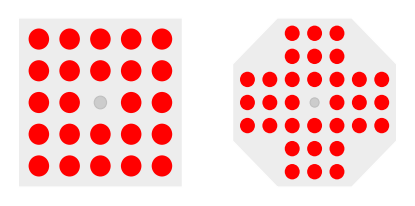

The rules for the game are very simple, pegs (or marbles in some versions) are jumped over each other in a similar way to how pieces in checkers move when they are capturing pieces. Moves can only be made horizontally and vertically, and each move removes exactly one peg from the board. The objective of the game is to be able to remove all but one piece from the board.

Example Game:

## Creating Multiway Graphs

Multiway graphs are graphs which represent all possible paths in a system. Each of the nodes in our multiway graphs represents a different game state which can be reached from the one previous, and each edge, or arrow, between nodes is a move.
In multiway graphs of peg solitaire, each movement down the graph removes exactly one peg from the game board, and no pegs can be added back, meaning the graph will only move downward and never loop.

```mathematica
samplegraph =multiwaygraph[{{1,3},{2,1},{2,2},{2,3},{3,2},{3,3},{3,4},{4,2}}, {0,1,1,1,1,1,1,1},{{1,4,6},{7,6,5},
{3,5,8},{4,3,2}}];
ListAnimate[Table[HighlightGraph[samplegraph, Table[If[Count[edge[[1]],1]>=i,edge, Nothing], {edge, EdgeList[samplegraph]} ]], {i, Reverse[Range[2,7]]}]]
```

To generate the graphs for peg solitaire, I first created a function which would create a graph of the game without visuals showing game states, shown here. This function was directly pulled from code in Steven Wolfram’s writing “Games and Puzzles as Multicomputational Systems”, which was the main jumping off point for this project and provided me with many of the resource functions I use such as Nest While Graph, Iterate TPS Move, and Peg Solitaire Graphics.

graphgen utilizes the resource functions NestWhileGraph and IterateTPSMove to generate a node diagram for my multiway graphs, which I will then put graphics over to show the board states at different points in the game. IterateTPSMove provides all the next possible moves given a move set and game state, and NestWhileGraph simply iterates this process over while there are possible moves left on the board.

```mathematica
graphgen[start_,moves_ ]:={{"[◼]", "NestWhileGraph"}}[
{{"[◼]", "IterateTPSMove"}}[moves],
{start},
UnsameQ@@#&,2]
```

To make my life easier, and my code more readable, I created a function which takes in a list of coordinate pairs ex: {{1,1},{1,2},{1,3}} and gives each of them “names” ex: {{1,1}->1,{1,2}->2,{1,3}->3} so that they are properly formatted for the IterateTPSMove and PegSolitaireGraphics functions.

```mathematica
coordnames[coords_] := MapIndexed[#1->#2[[1]]&,coords]
```

All of this built up to creating a base multiway graph function, this takes in a list of coordinate pairs, a starting board state, and a list of possible moves that can be made on the board and outputs a full multiway graph of the board.

```mathematica
multiwaygraph[coords_, start_, moves_] := Graph[graphgen[start, moves],VertexShapeFunction->(Inset[{{"[◼]", "PegSolitaireGraphics"}}[coordnames[coords]][
#2],#1,Center,#3]&),VertexSize->1.2,PerformanceGoal->"Quality",EdgeStyle->Gray,
GraphLayout->"LayeredDigraphEmbedding",AspectRatio->3]
```

```mathematica
multiwaygraph[{{1,3},{2,1},{2,2},{2,3},{3,2},{3,3},{3,4},{4,2}}, {0,1,1,1,1,1,1,1},{{1,4,6},{7,6,5},
{3,5,8},{4,3,2}}]
```

-Graphics-

### Removing “Duplicate” Board States Using Image Transformations

As I was looking at the multiway graphs of larger boards, I noticed that many of the board states were quite similar, just rotated or flipped, and I knew that if I could remove these duplicate boards it would make my graphs cleaner and more readable.

```mathematica
multiwaygraph[threecoords,{0,1,1,1,1,1,1,1,1}, threemoves ]
```

-Graphics-

My first idea on how to delete these duplicate boards was to analyze their images when put through peg solitaire graphs, but this turned out to be very computationally expensive and take a very long time which was unfortunate. 
I created three functions which work together to generate a list of “unique” board states given a list of states based on their image data. These only work on square and cross boards due to the way triangular boards are generated visually.

Due to the fact that I needed to rotate images, just using the == test function didn’t work, as during image rotation artifacts were created in the image which made the image data not exactly the same, so I had to create my own function to test image similarity using the image difference of the images.

```mathematica
compareImg[img1_, img2_]:=If[
  Length[DominantColors[ImageDifference[ImageRotate[img1, 90 Degree], img2]]] ==1 || 
Length[DominantColors[ImageDifference[ImageRotate[img1, 180 Degree], img2]]]==1 || 
Length[DominantColors[ImageDifference[ImageRotate[img1, 270 Degree], img2]]]==1 ||
Length[DominantColors[ImageDifference[ImageReflect[img1], img2]]]==1||
Length[DominantColors[ImageDifference[ImageReflect[img1, Left], img2]]]==1 ||
Length[DominantColors[ImageDifference[ImageRotate[ImageReflect[img1],90Degree], img2]]]==1 ||
Length[DominantColors[ImageDifference[ImageRotate[ImageReflect[img1],180Degree], img2]]]==1 ||
Length[DominantColors[ImageDifference[ImageRotate[ImageReflect[img1],270Degree], img2]]]==1,
True, False]
```

```mathematica
uniqueImg[img_, uniques_] := Which[Length[uniques] ==1, Not[compareImg[img, uniques[[1]]]],
Position[compareImg@@@Partition[Riffle[uniques,img, {2, -1, 2}],2],True] == {}, True, True, False]
```

```mathematica
getUnique[stateimglist_] := 
Block[{states = stateimglist, uniques = {stateimglist[[1]]}},
If[uniqueImg[#, uniques], AppendTo[uniques, #]]&/@states[[2;;]]; uniques]
```

Next, I created a new multiway graph function which removed duplicate boards using the image comparison function, like I mentioned above, it’s quite slow due to the amount of image manipulation it’s doing.

```mathematica
multiwayImageCheck[coordlist_, starting_, allmoves_] := Module[{coords = coordnames[coordlist], start = starting, moves = allmoves, graph, boardcoords},
graph = Graph[graphgen[start, moves],VertexShapeFunction->(Inset[{{"[◼]", "PegSolitaireGraphics"}}[coords][
#2],#1,Center,#3]&),VertexSize->1.2,PerformanceGoal->"Quality",EdgeStyle->Gray,
GraphLayout->"LayeredDigraphEmbedding",AspectRatio->3];
boardcoords = ReplacePart[VertexList[graph][[1]], Association[Reverse/@Normal[coords]]];
VertexContract[graph, Gather[VertexList[graph],compareImg[{{"[◼]", "PegSolitaireGraphics"}}[coordnames[boardcoords]][#1], {{"[◼]", "PegSolitaireGraphics"}}[coordnames[boardcoords]][#2]] ==True&]]
]
```

### Removing “Duplicate” Board States Using Matrix Transformations

I quickly realized that the image method of removing duplicate boards was not going to work, so I pivoted to using matrix transformations. Unfortunately this currently only works for square boards, as the matrix transformations for triangular and cross boards are not the same. This method is much faster than the image method which allows me to use it for larger boards without worrying about how long it will take.

Similarly to the way I implemented the image comparison functions, I have one function which compares two states and if they are the same, one function which takes in a board state and a list of unique boards and tests if the board is already represented, and a final function which creates a list of unique states from a list of all the states.

```mathematica
compareSqrList[list1_, list2_] := Module[{length = Sqrt[Length[list1]]},
lists1 = Partition[list1, length];
lists2 = Partition[list2, length];
If[Transpose @(Reverse/@lists1)==lists2 ||
Reverse/@(Transpose @lists1)==lists2 ||
Transpose @(Reverse/@(Transpose @(Reverse/@lists1)))==lists2 ||
Transpose @(Reverse/@(Transpose @lists1)) == lists2||
Reverse/@(Transpose @(Reverse/@lists1)) == lists2||
Transpose @lists1 ==lists2 ||
Reverse/@lists1 ==lists2
,True,False]
]
```

```mathematica
uniqueboard[board_, uniques_] := Which[Length[uniques] ==1, Not[compareSqrList[board, uniques[[1]]]],
Position[compareSqrList@@@Partition[Riffle[uniques,{board}, {2, -1, 2}],2],True] == {}, True, True, False]
```

```mathematica
getUniqueBoards[statelist_] := 
Block[{states = statelist, uniques = {statelist[[1]]}},
If[uniqueboard[#, uniques], AppendTo[uniques, #]]&/@states[[2;;]]; uniques]
```

Similar to the previous implementation of my multiway graph function,  this function only shows “unique” board states, but runs much faster due to the fact it utilizes matrix transformations. Unfortunately the draw back to this is that It only works on square boards

```mathematica
multiwayMatrixCheck[coordlist_, starting_, allmoves_] := Module[{coords = coordnames[coordlist], start = starting, moves = allmoves},
graph = Graph[graphgen[start, moves],VertexShapeFunction->(Inset[{{"[◼]", "PegSolitaireGraphics"}}[coords][
#2],#1,Center,#3]&),VertexSize->1.2,PerformanceGoal->"Quality",EdgeStyle->Gray,
GraphLayout->"LayeredDigraphEmbedding",AspectRatio->3];
boardcoords = ReplacePart[VertexList[graph][[1]], Association[Reverse/@Normal[coords]]];
VertexContract[graph, Gather[VertexList[graph],compareSqrList[#1,#2] ==True&]]
]
```

```mathematica
multiwayImageCheck[threecoords,{0,1,1,1,1,1,1,1,1}, threemoves]//Timing
```

{122.473,-Graphics-}

```mathematica
multiwayMatrixCheck[threecoords,{0,1,1,1,1,1,1,1,1}, threemoves]//Timing
```

{0.017181,-Graphics-}

### Generating All Possible Moves

As I worked more with the multiway graph functions, I wanted there to be an easier way for me to create a list of all the possible moves in a board as I’d been doing it all manually, so I created a function which, given a board’s coordinate pair list, would output all possible moves. 
To do this, I needed to be able to distinguish between triangle and square (or cross) boards, so I created a classifier function which could do this, and to create data for the neural network, I created a function which given a set of coordinates created a graph of what the board would look like.

```mathematica
makeimg[points_ ] := 
Graphics[{PointSize[Large],Point[Table[p,{p,points}]]}]
```

```mathematica
triangle =
```

```mathematica
square =
```

```mathematica
checkshape = Classify[<|"square" -> square, "triangle" ->triangle|>]
```

ClassifierFunction[…]

I then created a set of functions which together create the move lists for all types of boards by mapping through all the pegs in the board. I had to separate between triangle and square boards due to the fact that while on square boards diagonal moves are not allowed, on trianglular boards they are.

```mathematica
getNear[coords_ , peg_, shape_String:"square" ]/;shape=="square"&&Head[coords[[1]]]==List:= Delete[#, Position[#, peg]]&[Select[Table[Which[EuclideanDistance[peg, coord] == 1 && (coord[[1]] == peg[[1]] || coord[[2]] == peg[[2]]), coord],{coord, coords}], ListQ]]
```

```mathematica
getNear[coords_ , peg_, shape_String:"square"]/;shape=="triangle" &&Head[coords[[1]]]==List:= Delete[#, Position[#, peg]]&[Select[Table[Which[EuclideanDistance[peg, coord] < 2 || And[peg[[2]]==coord[[2]],EuclideanDistance[peg, coord] == 2], coord],{coord, coords}], ListQ]]
```

```mathematica
pegMoves[initalpeg_, coordlist_ /;Head[coordlist[[1]]]==List]:=Module[{peg = initalpeg, coords = coordlist, moves = {}, peg2s, peg3s},
peg2s = getNear[coords, peg, checkshape[makeimg[coords]]];
peg3s = Table[{peg2[[1]]+(peg2[[1]] - peg[[1]]), peg2[[2]]+(peg2[[2]]-peg[[2]])}, {peg2, peg2s}];
Select[Table[If[Position[coords,peg3s[[i]]] != {},{peg, peg2s[[i]], peg3s[[i]]}], {i, Range[Length[peg2s]]}], ListQ]
]
```

```mathematica
allMoves[coordlist_/;Head[coordlist[[1]]]==List] := Module[{coords = coordlist, moves = {}},
ResourceFunction["JoinTo"][moves, pegMoves[#, coords] /. coordnames[coords] &/@ coords];
DeleteDuplicates[Flatten[moves,1], Length[#1∪#2] ==3 &]
]
```

### Manipulating Graphs

```mathematica
cropGraph[fullgraph_, maxpins_,minpins_ ,coords_, xsquish_:1,ysquish_:2, size_:1.2] :=Graph[Graph[Cases[Table[If[ Position[Select[Table[If[Length[Position[vertex,1]]<=maxpins&&Length[Position[vertex,1]]>=minpins,vertex], {vertex, VertexList[fullgraph]}],ListQ],edge[[1]]]!={}, edge],{edge, EdgeList[fullgraph]}], Except[Null]]],VertexShapeFunction->(Inset[{{"[◼]", "PegSolitaireGraphics"}}[coordnames[coords]][
#2],#1,Center,#3]&),VertexSize->size,PerformanceGoal->"Quality",EdgeStyle->Gray,
GraphLayout->"LayeredDigraphEmbedding",AspectRatio->3, VertexCoordinates->Rule @@@Partition[Riffle[VertexList[fullgraph],Table[{(VertexCoordinates/. AbsoluteOptions[fullgraph,VertexCoordinates])[[i]][[1]]/xsquish,(VertexCoordinates/. AbsoluteOptions[fullgraph,VertexCoordinates])[[i]][[2]]/ysquish },{i, Range[Length[(VertexCoordinates/. AbsoluteOptions[fullgraph,VertexCoordinates])]]}]],2]]
```

```mathematica
Manipulate[cropGraph[-Graphics-,max,min,{{0,0},{-1,1},{1,1},{-2,2},{0,2},{2,2},{-3,3},{-1,3},{1,3}, {3,3}}],{max,9,min,1,Appearance->"Labeled"},{min,2,max,1,Appearance->"Labeled"}, ContinuousAction->False, SaveDefinitions->True]
```

```mathematica
manipulateGraph[fullgraph_, coords_, xsquish_:1,ysquish_:2, size_:1.2] :=Graph[fullgraph,VertexShapeFunction->(Inset[{{"[◼]", "PegSolitaireGraphics"}}[coordnames[coords]][
#2],#1,Center,#3]&),VertexSize->size,PerformanceGoal->"Quality",EdgeStyle->Gray,
GraphLayout->"LayeredDigraphEmbedding",AspectRatio->3, VertexCoordinates->Rule @@@Partition[Riffle[VertexList[fullgraph],Table[{(VertexCoordinates/. AbsoluteOptions[fullgraph,VertexCoordinates])[[i]][[1]]/xsquish,(VertexCoordinates/. AbsoluteOptions[fullgraph,VertexCoordinates])[[i]][[2]]/ysquish },{i, Range[Length[(VertexCoordinates/. AbsoluteOptions[fullgraph,VertexCoordinates])]]}]],2]]
```

## Analyzing 3 by 3 Boards

```mathematica
(* all "starting board" states which lead to a multiway graph longer than 2 *)
threecoords = {{1,1},{2,1},{3,1},{1,2},{2,2},{3,2},{1,3},{2,3},{3,3}};
threemoves = allMoves[threecoords];
allthrees = SortBy[Select[Table[If[VertexCount[multiwayMatrixCheck[threecoords, state, threemoves]]>2, multiwayMatrixCheck[threecoords, state, threemoves]], {state, Table[perm, {perm, getUniqueBoards[Flatten[Permutations[Join[Range[#]/. _Integer->1, Range[9-#]/. _Integer->0 ]]&/@ Range[9],1]]}]}],GraphQ], VertexCount];
solutionthrees = SortBy[Select[Table[If[VertexCount[multiwayMatrixCheck[threecoords, state, threemoves]]>2 && Length[Position[VertexList[multiwayMatrixCheck[threecoords, state, threemoves]][[-1]],1]]==1, multiwayMatrixCheck[threecoords, state, threemoves]], {state, Table[perm, {perm, getUniqueBoards[Flatten[Permutations[Join[Range[#]/. _Integer->1, Range[9-#]/. _Integer->0 ]]&/@ Range[9],1]]}]}],GraphQ], VertexCount];
```

same number of boards when there’s 1 hole and when there is 9, 2 - 7, 3 - 6, 4 - 5

```mathematica
ListAnimate[Table[Which[Length[row]>16, GraphicsGrid[Partition[row,6]],Length[row]>3, GraphicsGrid[Partition[row,4]], True,GraphicsGrid[{row}]],{row,Table[Table[{{"[◼]", "PegSolitaireGraphics"}}[coordnames[threecoords]][perm], {perm, getUniqueBoards[Permutations[Join[Range[9-holes]/. _Integer->1, Range[holes]/. _Integer->0 ]]]}],{holes, 1,8,1} ] }]]
```

### All Possible Multiway Graphs

```mathematica
ListAnimate[Table[Which[Length[row]>=12, GraphicsGrid[Partition[row,4]], Length[row]>=6, GraphicsGrid[Partition[row,3]],True, GraphicsGrid[{row}]],{row,Table[Select[allthrees, VertexCount[#]==moves&],{moves, 3,10,1}]}]]
```

```mathematica
(* all "starting board" states which lead to a solution *)
SortBy[Select[Table[If[VertexCount[multiwayMatrixCheck[threecoords, state, threemoves]]>1 && Length[Position[VertexList[multiwayMatrixCheck[threecoords, state, threemoves]][[-1]],1]]==1, multiwayMatrixCheck[threecoords, state, threemoves]], {state, Table[perm, {perm, getUniqueBoards[Flatten[Permutations[Join[Range[#]/. _Integer->1, Range[9-#]/. _Integer->0 ]]&/@ Range[9],1]]}]}],GraphQ], VertexCount]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### 3 By 3 Boards with Holes

```mathematica
holeBoardPerms[holes_Integer, boardsize_Integer/;IntegerQ[Sqrt[boardsize]],blanks_:1] := 
getUniqueBoards[Permutations[Join[Range[boardsize-holes-blanks]/._Integer->1, Range[holes]/._Integer->3, Range[blanks]/._Integer->0]]]
```

```mathematica
holeBoardCoords[coords_, state_] :=Select[coordnames[threecoords],state[[#[[2]]]]!=3&]
```

```mathematica
(* multiway graph creater for boards with holes (takes in coordlist WITH names) *)
multiwayHoles[coordlist_, starting_, allmoves_] := Module[{coords = coordlist, start = starting, moves = allmoves},
graph = Graph[graphgen[start, moves],VertexShapeFunction->(Inset[{{"[◼]", "PegSolitaireGraphics"}}[coords][
#2],#1,Center,#3]&),VertexSize->1.2,PerformanceGoal->"Quality",EdgeStyle->Gray,
GraphLayout->"LayeredDigraphEmbedding",AspectRatio->3];
boardcoords = ReplacePart[VertexList[graph][[1]], coords];
VertexContract[graph, Gather[VertexList[graph],compareSqrList[#1,#2] ==True&]]
]
```

```mathematica
GraphicsRow[Select[Table[If[VertexCount[multiwayHoles[holeBoardCoords[threecoords, perm], perm, allMoves[holeBoardCoords[threecoords, perm]]]]>=3,multiwayHoles[holeBoardCoords[threecoords, perm], perm, allMoves[holeBoardCoords[threecoords, perm]]]],{perm,holeBoardPerms[1,9]}], GraphQ]]
```

-Graphics-

## Expanding 3 by 3’s to Larger Boards

Initializing some variables to make the code cleaner later on!

```mathematica
threecoords = ;
fourcoords = ;
fourmoves = ;
fivecoords = ;
fivemoves = ;
```

I wanted to look at how the multiway graphs of previously unsolvable 3 by 3’s would look if expanded to larger board sizes, so I first tried 5 by 5’s for which I simply added an extra empty row / column on each side of the board state list to expand the board out, below you can see a graphic of all the possible 3 by 3 boards which don’t end in a solution expanded out to a 5 by 5 board.

```mathematica
getFiveCoords[graph_] :=Flatten[Prepend[Append[Table[Flatten[Prepend[Append[Partition[VertexList[graph][[1]],3][[i]],0],0]],{i, Range[3]}],{0,0,0,0,0}],{0,0,0,0,0}]]
```

Three by Threes expanded to 5 x 5 boards

I then also wanted to test this idea on 4 by 4’s, which was a little more complicated due to the fact there were 4 different ways which a 4 by 4 could be positioned in, or “on” a 3 by 3 board. I created a function where you can specify which areas you want an extra row / column to be added, top or bottom and right or left, and a function which could work for all of those cases.

```mathematica
getFourCoords[graph_, tb_, rl_]/;tb==1 && rl==1 :=Flatten[Append[Table[Flatten[Append[Partition[VertexList[graph][[1]],3][[i]],0],0],{i, Range[3]}],{0,0,0,0}]]
getFourCoords[graph_, tb_, rl_]/;tb==1 && rl==0 :=Flatten[Append[Table[Flatten[Prepend[Partition[VertexList[graph][[1]],3][[i]],0],0],{i, Range[3]}],{0,0,0,0}]]
getFourCoords[graph_, tb_, rl_]/;tb==0 && rl==1 :=Flatten[Prepend[Table[Flatten[Prepend[Partition[VertexList[graph][[1]],3][[i]],0],0],{i, Range[3]}],{0,0,0,0}]]
getFourCoords[graph_, tb_, rl_]/;tb==0 && rl==0 :=Flatten[Prepend[Table[Flatten[Append[Partition[VertexList[graph][[1]],3][[i]],0],0],{i, Range[3]}],{0,0,0,0}]]
```

For this essay, I’ll focus in on this 3 by 3 board, and show it’s possible 4 by 4 multiway graphs

```mathematica
graph = -Graphics-;
```

```mathematica
GraphicsRow[Table[multiwayMatrixCheck[fourcoords, state, allMoves[fourcoords]], {state, Table[getFourCoords[graph, perm[[1]],perm[[2]]],{perm, {{0,0},{0,1},{1,0},{1,1}}}]}]]
```

-Graphics-

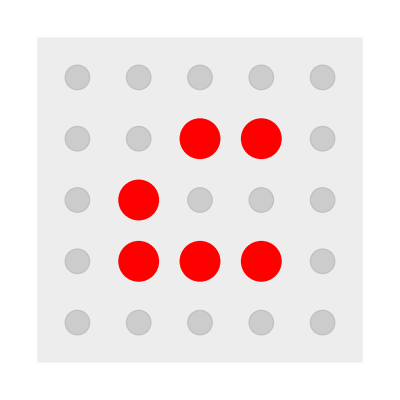
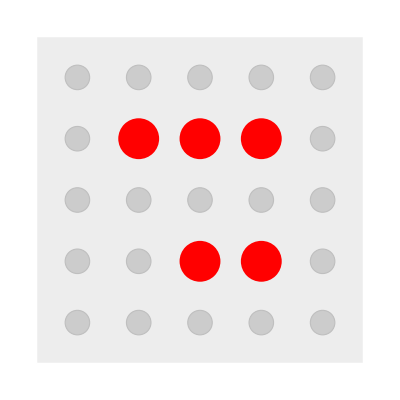
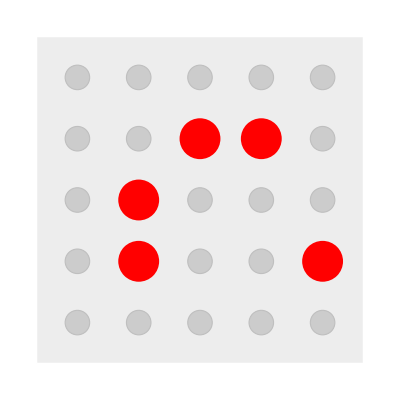
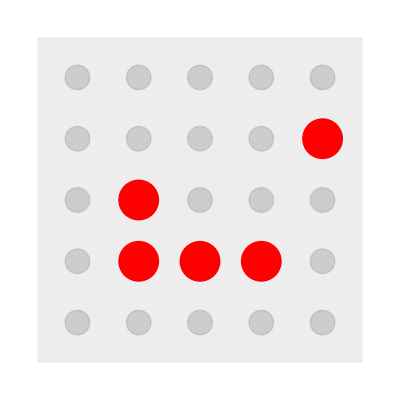
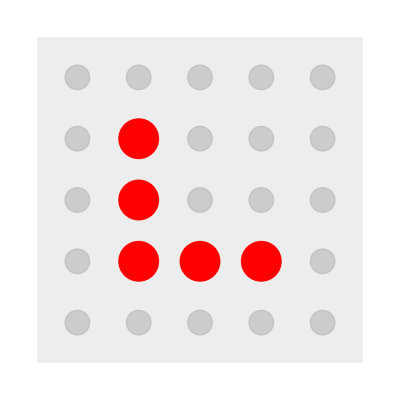
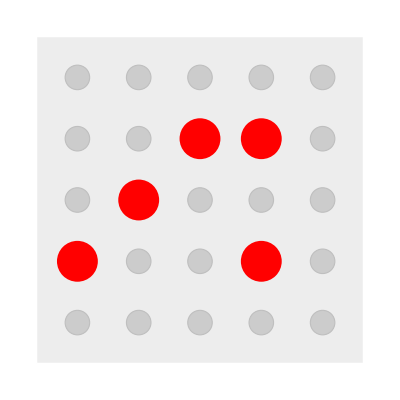
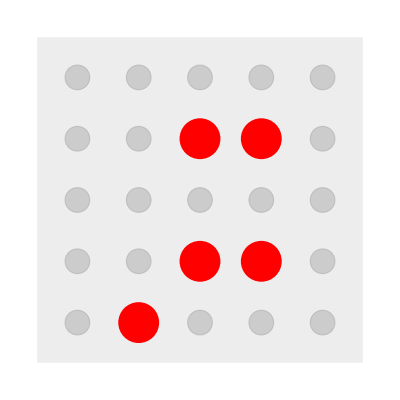
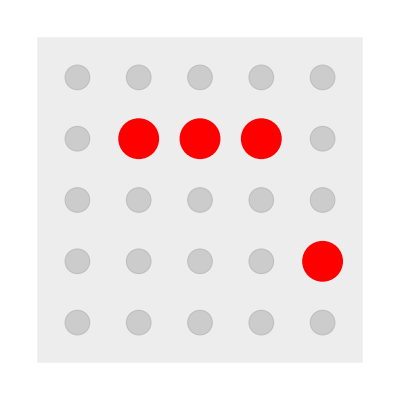

```mathematica
fivegraph = multiwaygraph[fivecoords, getFiveCoords[-Graphics-], allMoves[fivecoords]];
manipulateGraph[fivegraph, fivecoords,1.5,6,1.5]
```

### Comparing 4 x 4 and 5 x 5 Boards

```mathematica
fourToFive[list_, tb_, rl_]/;tb==1 && rl==1:=Flatten[Append[Table[Append[Partition[list,4][[i]],0],{i, Range[4]}],{0,0,0,0,0}]]
fourToFive[list_, tb_, rl_]/;tb==1 && rl==0:=Flatten[Append[Table[Prepend[Partition[list,4][[i]],0],{i, Range[4]}],{0,0,0,0,0}]]
fourToFive[list_, tb_, rl_]/;tb==0 && rl==1:=Flatten[Prepend[Table[Append[Partition[list,4][[i]],0],{i, Range[4]}],{0,0,0,0,0}]]
fourToFive[list_, tb_, rl_]/;tb==0 && rl==0:=Flatten[Prepend[Table[Prepend[Partition[list,4][[i]],0],{i, Range[4]}],{0,0,0,0,0}]]
```

```mathematica
fourFiveGraphHighlight[fivegraph_, fourgraph_, tb_, rl_, xsquish_:1, ysquish_:2, size_:1.5] :=manipulateGraph[HighlightGraph[fivegraph,DeleteCases[Table[If[Position[Intersection[VertexList[fivegraph], Table[fourToFive[VertexList[fourgraph][[i]],tb,rl],{i, Range[Length[VertexList[fourgraph]]]}]],EdgeList[fivegraph][[i]][[2]]]!={},EdgeList[fivegraph][[i]]],{i,Length[EdgeList[fivegraph]]}],Null]], fivecoords,xsquish,ysquish,size]
```

```mathematica
Manipulate[fourFiveGraphHighlight[-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,graph[[1]],graph[[2]][[1]],graph[[2]][[2]],.5,2],{{graph,{multiwayMatrixCheck[fourcoords, Range[16]/. _Integer->0, fourmoves],{1,0}} ," "},{{-Graphics-,{1,0}}->{{"[◼]", "PegSolitaireGraphics"}}[coordnames[fourcoords]][VertexList[-Graphics-][[1]]],{-Graphics-,{1,1}}->{{"[◼]", "PegSolitaireGraphics"}}[coordnames[fourcoords]][VertexList[-Graphics-][[1]]],{-Graphics-,{0,1}}->{{"[◼]", "PegSolitaireGraphics"}}[coordnames[fourcoords]][VertexList[-Graphics-][[1]]],{-Graphics-,{0,0}}->{{"[◼]", "PegSolitaireGraphics"}}[coordnames[fourcoords]][VertexList[-Graphics-][[1]]]}}, SaveDefinitions->True]
```

Part::partd: Part specification … is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

VertexList::graph: A graph object is expected at position 1 in ….

## Extensions

Analyzing larger boards

Analyzing triangular boards

Simplifying larger boards by using smaller boards

## References

(n.d.). Peg Solitaire. Wikipedia. Retrieved July 10, 2024, from https://en.wikipedia.org/wiki/Peg_solitaire

Wolfram, S. (2022, June 8). Games and Puzzles as Multicomputational Systems. Stephen Wolfram Writings. Retrieved July 10, 2024, from https://writings.stephenwolfram.com/2022/06/games-and-puzzles-as-multicomputational-systems/